## Get the Data

```mathematica
GEdata=Import["~/Research/SIR/Source/FRO_adm1.kmz","Data"];
```

```mathematica
names=Flatten["PlacemarkNames"/.GEdata]
```

{Eysturoyar,Norderøerne,Sandoyar,Streymoyar,Suðuroyar,Vågø}

```mathematica
(Geom=Flatten["Geometry"/.GEdata])//Length
```

27

```mathematica
gdata=SortBy[Geom,Length@#[[1,1]]&]//Reverse;
```

```mathematica
names=Range[8]/.{1->"Esturoy",2->"Bordoy",3-> "Suduroy",4->"Streymoy",5->"Vagar",6->"Sandoy",7->"Kalsoy",8->"Svinoy"}
```

{Esturoy,Bordoy,Suduroy,Streymoy,Vagar,Sandoy,Kalsoy,Svinoy}

```mathematica
pops = {"Streymoy"->22450,"Esturoy"->10726,"Vagar"-> 3064,"Suduroy"->4680,"Sandoy"->1283,"Bordoy"-> 4940+596+129,"Kalsoy"-> 94, "Svinoy"->32}
```

{Streymoy→22450,Esturoy→10726,Vagar→3064,Suduroy→4680,Sandoy→1283,Bordoy→5665,Kalsoy→94,Svinoy→32}

```mathematica
popsVis = {"Streymoy"->100,"Esturoy"->130,"Vagar"-> 94,"Suduroy"->60,"Sandoy"->50,"Bordoy"-> 80,"Kalsoy"-> 42, "Svinoy"->32}
```

{Streymoy→100,Esturoy→130,Vagar→94,Suduroy→60,Sandoy→50,Bordoy→80,Kalsoy→42,Svinoy→32}

```mathematica
card={"Esturoy"->1,"Bordoy"->2,"Suduroy"->3,"Streymoy"->4,"Vagar"->5,"Sandoy"->6,"Kalsoy"->7,"Svinoy"->8}
```

{Esturoy→1,Bordoy→2,Suduroy→3,Streymoy→4,Vagar→5,Sandoy→6,Kalsoy→7,Svinoy→8}

```mathematica
Graphics[MapThread[Tooltip[#1,Grid[{{#2,#3}},Frame->All]]&,{gdata[[;;8]],names,names/.pops}]]
```

-Graphics-

```mathematica
Total[names/.pops]
```

548

## Simply Scale Everything

```mathematica
xmin=Map[Min[#[[1,1,All,2]]]&,gdata[[;;8]]]
```

{-7.24167,-6.71198,-7.00156,-7.26198,-7.46667,-6.95156,-6.81823,-6.41667}

```mathematica
xmax=Map[Max[#[[1,1,All,2]]]&,gdata[[;;8]]]
```

{-6.60052,-6.40469,-6.66458,-6.73177,-7.06458,-6.63385,-6.65833,-6.28385}

```mathematica
ymin=Map[Min[#[[1,1,All,1]]]&,gdata[[;;8]]]
```

{62.0542,62.1667,61.3937,61.9375,62.0208,61.7521,62.225,62.2313}

```mathematica
ymax=Map[Max[#[[1,1,All,1]]]&,gdata[[;;8]]]
```

{62.3396,62.3917,61.6521,62.2373,62.1583,61.9146,62.3729,62.3063}

```mathematica
gxmin = Min[xmin]
```

-7.46667

```mathematica
gxmax = Max[xmax]
```

-6.28385

```mathematica
gymin=Min[ymin]
```

61.3937

```mathematica
gymax=Max[ymax]
```

62.3917

### Bounding Box

```mathematica
GeoDistance[{Min[xmin],Min[ymin]},{Max[xmax],Max[ymax]}]
```

106.316 mi

```mathematica
GeoDistance[{Min[xmin],Min[ymin]},{Max[xmax],Min[ymin]}]
```

81.28 mi

```mathematica
GeoDistance[{Min[xmin],Max[ymax]},{Max[xmax],Max[ymax]}]
```

81.28 mi

```mathematica
GeoDistance[{Min[xmin],Min[ymin]},{Min[xmin],Max[ymax]}]
```

68.4452 mi

```mathematica
GeoDistance[{Max[xmax],Min[ymin]},{Max[xmax],Max[ymax]}]
```

68.6147 mi

```mathematica
{gxmin->5,gxmax->5+81.28,gymin->5,gymax->5+68.6147}
```

{-7.46667→5,-6.28385→86.28,61.3937→5,62.3917→73.6147}

```mathematica
XTransform[x_]:=(x-gxmin)*81.28+5
```

```mathematica
XTransform[gxmax]
```

101.139

```mathematica
YTransform[y_]:=(y-gymin)*68.6147+5
```

```mathematica
YTransform[gymax]
```

73.4718

## Export

```mathematica
xmin=XTransform/@Map[Min[#[[1,1,All,2]]]&,gdata[[;;8]]]
```

{23.288,66.341,42.8037,21.637,5.,46.8676,57.705,90.344}

```mathematica
xmax=XTransform/@Map[Max[#[[1,1,All,2]]]&,gdata[[;;8]]]
```

{75.4004,91.3177,70.1933,64.7323,37.6813,72.691,70.7013,101.139}

```mathematica
ymin=YTransform/@Map[Min[#[[1,1,All,1]]]&,gdata[[;;8]]]
```

{50.3142,58.0336,5.,42.3093,48.0271,29.587,62.0359,62.4649}

```mathematica
ymax=YTransform/@Map[Max[#[[1,1,All,1]]]&,gdata[[;;8]]]
```

{69.8982,73.4718,22.7256,62.8824,57.4617,40.737,72.1853,67.6111}

```mathematica
GeneralData=Thread[{Range[8],names,"Island",xmin,xmax,ymin,ymax,names/.pops}];
```

```mathematica
GeneralDataVis=Thread[{Range[8],names,"Island",xmin,xmax,ymin,ymax,names/.popsVis}];
```

```mathematica
Export["~/Research/SIR/Source/GeneralData.csv",GeneralData]
```

~/Research/SIR/Source/GeneralData.csv

```mathematica
Export["~/Research/SIR/Source/GeneralDataVis.csv",GeneralDataVis]
```

~/Research/SIR/Source/GeneralDataVis.csv

```mathematica
gdataTransform =Map[#[[1,1]]/.{{x_,y_}->{XTransform[y],YTransform[x]}}&,gdata];
```

```mathematica
Take[gdataTransform[[;;8]][[1]],{1,-1,2}]//Length
```

909

```mathematica
gdataTransform[[;;8]][[1]]//Length
```

1818

```mathematica
files = MapThread[Export[StringJoin["~/Research/SIR/Source/",#1,".csv"],Take[#2,{1,-1,2}]]&,{names,gdataTransform[[;;8]]}]
```

{~/Research/SIR/Source/Esturoy.csv,~/Research/SIR/Source/Bordoy.csv,~/Research/SIR/Source/Suduroy.csv,~/Research/SIR/Source/Streymoy.csv,~/Research/SIR/Source/Vagar.csv,~/Research/SIR/Source/Sandoy.csv,~/Research/SIR/Source/Kalsoy.csv,~/Research/SIR/Source/Svinoy.csv}

## Polygon Triangulation

```mathematica
getPolygondata[data_]:=Module[
{
mr = DiscretizeRegion[Polygon[data],MaxCellMeasure->{"Area"->Infinity}],
coordinates,cells
},
coordinates=MeshCoordinates[mr];
cells=MeshCells[mr,2][[All,1]];
Map[Flatten[coordinates[[#]]]&,cells]
]
```

```mathematica
readDataTriangulateExport[filename_]:=Module[
{
datain = Import[filename],
dataout,
fileout = StringReplace[filename,d__~~"/"~~n__~~".csv":>d<>"/"<>n<>"Polygon"<>".csv"]
},
dataout=getPolygondata[datain];
Export[fileout,dataout]
]
```

```mathematica
readDataTriangulateExport/@files
```

{~/Research/SIR/Source/EsturoyPolygon.csv,~/Research/SIR/Source/BordoyPolygon.csv,~/Research/SIR/Source/SuduroyPolygon.csv,~/Research/SIR/Source/StreymoyPolygon.csv,~/Research/SIR/Source/VagarPolygon.csv,~/Research/SIR/Source/SandoyPolygon.csv,~/Research/SIR/Source/KalsoyPolygon.csv,~/Research/SIR/Source/SvinoyPolygon.csv}

## Projection

```mathematica
GeoGridPosition[GeoPosition[{-6.60052061080933,62.339584350586}],"Stereographic"]
```

GeoGridPosition[{1.20431,-0.157336},Stereographic]

### Bounding Box

```mathematica
GeoDistance[{Min[xmin],Min[ymin]},{Max[xmax],Max[ymax]}]
```

106.316 mi

```mathematica
GeoDistance[{Min[xmin],Min[ymin]},{Max[xmax],Min[ymin]}]
```

81.28 mi

```mathematica
GeoDistance[{Min[xmin],Max[ymax]},{Max[xmax],Max[ymax]}]
```

81.28 mi

```mathematica
GeoDistance[{Min[xmin],Min[ymin]},{Min[xmin],Max[ymax]}]
```

68.4452 mi

```mathematica
GeoDistance[{Max[xmax],Min[ymin]},{Max[xmax],Max[ymax]}]
```

68.6147 mi

### Distances

```mathematica
distances = Map[UnitConvert[GeoDistance[#[[1]],#[[2]]],"Miles"][[1]]&,Partition[gdata2[[1,1,1]],2,2,1]];
```

## Test

```mathematica
data = Import["~/Research/SIR/Source/Esturoy.csv"];
```

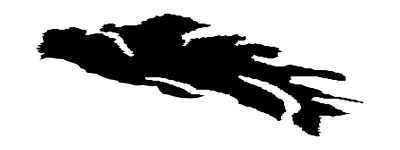

```mathematica
Graphics[Polygon[data]]
```

```mathematica
data = Import["~/Research/SIR/Source/Bordoy.csv"];
```

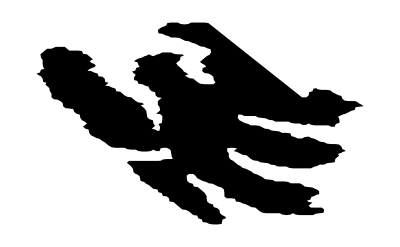

```mathematica
Graphics[Polygon[Drop[data,50]]]
```

```mathematica
data = Import["~/Research/SIR/Source/Esturoy.csv"];
```

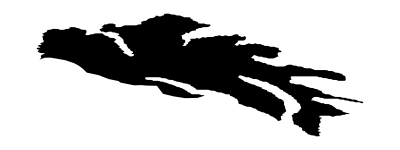

```mathematica
Graphics[Polygon[data]]
```

```mathematica
data//Length
```

909

```mathematica
data[[-1]]
```

{44.5817,69.8626}

```mathematica
{44.5817,69.8626}
```

```mathematica
{44.2853,69.8982}
```

```mathematica
{153,102,51}/255//N
```

{0.6,0.4,0.2}

```mathematica
{51,102,0}/255//N
```

{0.2,0.4,0.}

```mathematica
N@77/255
```

0.301961